```mathematica
(*Generates the plots in the paper.*)
```

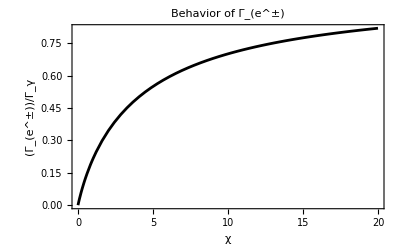

```mathematica
Plot[χ^3/(6NIntegrate[InverseFunction[#*Sqrt[1-#^-2]-ArcTan[Sqrt[#^2-1]]&][χ-rhop]*rhop,{rhop,0,χ}]),{χ,0,20},PlotRange->All,Axes->False,PlotStyle->Black,Frame->{{True,False},{True,False}},FrameLabel->{χ,Rotate[Subscript[Γ,Superscript[e,"±"]]/Subscript[Γ,γ],-Pi/2]},PlotLabel->Row[{"Behavior of ",Subscript[Γ,Superscript[e,"±"]]}]]
```

```mathematica
(*The integral in Γ is computationally expensive, so we interpolate the integrand and integrate that interpolation.*)
σ[vcom_]:=If[TrueQ[vcom==0],0,3(1-vcom)^2*((3-vcom^4)Log[(1+vcom)/(1-vcom)]/vcom-2(2-vcom^2))/(32vcom)]
vcomaux=Sqrt[(γp*γm(1-vp*vm)-1)/(γp*γm(1-vp*vm)+1)]/.{γp->1/Sqrt[1-vp^2],γm->1/Sqrt[1-vm^2]};
vcom[vpa_,vma_]:=vcomaux/.{vp->vpa,vm->vma}
velocaux=(#/Sqrt[1+#^2]&[InverseFunction[#-ArcTan[#]&][#]])&;
veloc=Interpolation[Table[{i,N[velocaux[i]]},{i,Range[0,20,.001]}]];
integrand=Interpolation[ParallelTable[{rhop,Quiet[NIntegrate[Chop[σ[vcom[#1,#2]]Abs[#1-#2]rhop1*rhop2/rhop^3&[veloc[rhop-rhop1],veloc[rhop-rhop2]]],{rhop1,0,rhop},{rhop2,0,rhop}]]},{rhop,Range[0,20,.05]}]];
```

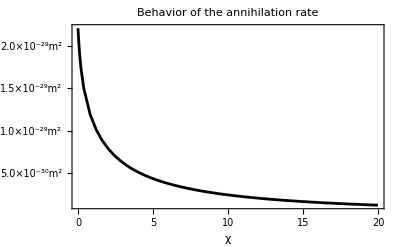

```mathematica
Plot[6.65*10^-29*8Integrate[integrand[rhop],{rhop,0,chi}]/chi^2,{chi,0,20},PlotRange->All,Axes->False,PlotStyle->Black,Frame->{{True,False},{True,False}},FrameLabel->{χ,Rotate[Row[{Subscript[Γ,"ann"],V}],-Pi/2]},PlotLabel->"Behavior of the annihilation rate",FrameTicks->{Automatic,{#,Row[{NumberForm[#,{2,1}],Superscript[" m",2]}]}&/@Range[5.*10^-30,2.*10^-29,5.*10^-30]}]
```

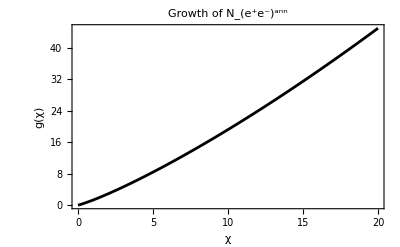

```mathematica
Plot[χ^5/(48NIntegrate[InverseFunction[#*Sqrt[1-#^-2]-ArcTan[Sqrt[#^2-1]]&][χ-rhop]*rhop,{rhop,0,χ}]*Integrate[integrand[rhop],{rhop,0,χ}]),{χ,0,20},PlotRange->All,Axes->False,PlotStyle->Black,Frame->{{True,False},{True,False}},FrameLabel->{χ,Rotate[Row[{g,"(χ)"}],-Pi/2]},PlotLabel->Row[{"Growth of ",Subsuperscript[N,Row[{Superscript[e,"+"],Superscript[e,"-"]}],"ann"]}]]
```

```mathematica
(*All quantities are calculated in natural units ℏ=c=ϵ0=1 and given in powers of eV.
Quantities without a listed unit are dimensionless.*)
atilde=.7;
modelK=1;
Ecrit=8.471*10^11;(*eV^2*)
echarge=.3028;
emass=5.11*10^5;(*eV*)
σT=1.708*10^-15;(*eV^-2*)
```

```mathematica
(*Nγeqold is the equilibrium value of Nγ, calculated without incorporating Schwinger production. Nγeq gives the value including Schwinger production and includes a check: the second number should be 1.*)
Δr[μ_,αμ_]:=Sqrt[5]/(μ*αμ)
vol[μ_,αμ_]:=2Pi^2*Sqrt[5]Δr[μ,αμ]^3
Γe[μ_,αμ_]:=1/Δr[μ,αμ]
NSchwinger[μ_,αμ_]:=3Pi^2*Ecrit^2*vol[μ,αμ]/(4μ)
ΓSchwinger[Nγ_,μ_,αμ_]:=Sum[echarge^2*Ecrit^2*vol[μ,αμ]/(4Sqrt[3]Pi)*(Nγ/(NSchwinger[μ,αμ]*n^2))^(1/3)*E^(-3(Nγ/(NSchwinger[μ,αμ]*n^2))^(-1/3)),{n,1,5}]
C1[μ_,αμ_]:=(8/25)αμ^2
Nγeqold[μ_,αμ_]:=atilde*αμ^8*μ/(48*C1[μ,αμ]*6.957*10^-65*modelK^2*(μ*10^5)^5)
Nγeq[μ_,αμ_]:=Quiet[If[#[[2]]>=1,{#[[1]],#[[1]]/Nγeqold[μ,αμ]},Indeterminate]&[{Nγ,Nγ^2*(1-8echarge^2*ΓSchwinger[Nγ,μ,αμ]/(emass*μ^2*vol[μ,αμ]*Γe[μ,αμ]))/Nγeqold[μ,αμ]^2}/.FindRoot[Nγ^2*(1-8echarge^2*ΓSchwinger[Nγ,μ,αμ]/(emass*μ^2*vol[μ,αμ]*Γe[μ,αμ]))-Nγeqold[μ,αμ]^2,{Nγ,Nγeqold[μ,αμ]}]]]
Nγeq[10^-5,.02]
```

{4.19242×10^47,1.}

```mathematica
(*Interpolations of the data in figure 2.*)
array=ParallelTable[{{mp,a},Quiet[Log[10,First[.5*10^mp*Γe[10^mp,a]Nγeq[10^mp,a]*2434]/.First[Indeterminate]->1]]},{mp,-8,-2,.25},{a,.02,.03,.0005}];
borderfunc=Interpolation[First[SortBy[#,First]]&/@GatherBy[Table[SortBy[Select[array[[i]],#[[-1]]>0&],#[[1,2]]&][[-1,1]],{i,1,Length[array]}],Last],Method->"Spline"]
interiorfunc=Interpolation[{#[[1,1,1]],Mean[Last/@#]}&/@GatherBy[Select[Flatten[array,1],#[[-1]]>0&],#[[1,1]]&]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

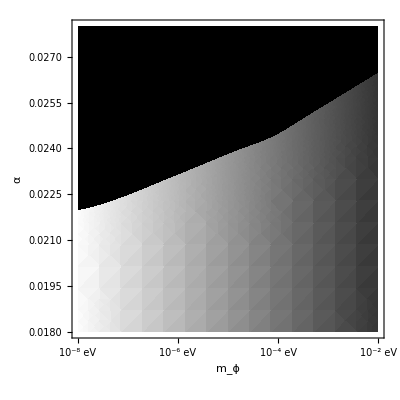
-Graphics-Stable and Unstable Regions of Parameter Space

```mathematica
(*Black and white version of figure 2, for publication.*)
cfbw=(If[#==0,Black,GrayLevel[(#-Floor[Min[Select[Last/@Flatten[array,1],#>0&]],5])/(Ceiling[Max[#],5]-Floor[Min[#],5]&[Select[Last/@Flatten[array,1],#>0&]])]]&);
Labeled[FullGraphics@GraphicsRow[{DensityPlot[interiorfunc[mp],{mp,-8,-2},{a,.018,.028},RegionFunction->Function[{mp,a},a≤borderfunc[mp]],Epilog->RegionPlot[a≥borderfunc[mp],{mp,-8,-2},{a,.018,.028},PlotStyle->{Black,PatternFilling["Diamond",ImageScaled[1/30]]},BoundaryStyle->None][[1]],FrameTicks->{{#,Row[{Superscript[10,#]," eV"}]}&/@Table[i,{i,-8,-2,2}],Automatic},FrameLabel->{Subscript[m,ϕ],Rotate[α,-Pi/2]},ColorFunctionScaling->False,ColorFunction->cfbw],ImageCrop[ImageCrop[Graphics[{White,Rectangle[{0,0},{.01,-.1}],Black,PatternFilling["Diamond",ImageScaled[1/15]],Rectangle[{-.018,0},{-.011,-.007}],PatternFilling[Graphics[Rectangle[]]],Text["Unstable",{.006,-.005}],Inset[BarLegend[{cfbw,{Floor[Min[#],5],Ceiling[Max[#],5]}&[Select[Last/@Flatten[array,1],#>0&]]},LegendLabel->Superscript[L,eq],Ticks->({#,Row[{Superscript["10",#]," erg/s"}]}&/@(Table[i,{i,Floor[Min[#],5],Ceiling[Max[#],5],5}]&[Select[Last/@Flatten[array,1],#>0&]]))],{0,.07}]},ImageSize->Medium]],{150,600},Top,Padding->White]}],"Stable and Unstable Regions of Parameter Space",Top]
```

```mathematica
(*Data for figure 3.*)
array2=Table[{{mp,a},Quiet[1/Sqrt[1-8echarge^2*ΓSchwinger[#,10^mp,a]/(emass*(10^mp)^2*vol[10^mp,a]*Γe[10^mp,a])]&[First[Nγeq[10^mp,a]]/.First[Indeterminate]->Indeterminate]]},{mp,-8,-2,.25},{a,.018,.028,.0005}];
```

```mathematica
(*Black and white version of figure 3, for publication.*)
Interpolation[Select[Flatten[array2-Table[{0,1},{mp,-8,-2,.25},{a,.02,.03,.0005}],1],NumberQ[Last[#]]&]];
Labeled[ImageCrop[Plot3D[%[mp,a],{mp,-8,-2},{a,.018,.028},RegionFunction->Function[{mp,a},a≤borderfunc[mp]],PlotRange->All,AxesLabel->{Subscript[m,ϕ],α,Rotate[Row[{Superscript[L,eq]/Superscript[L,"eq,RK"],-1}],.05]},ViewPoint->{-.2,-1.3,1.3},AxesEdge->{{-1,-1},{1,-1},{-1,1}},Boxed->{Back,Left},Ticks->{{#,Row[{Superscript[10,#]," eV"}]}&/@Table[i,{i,-8,-2,3}],Automatic,Automatic},Mesh->None,ColorFunction->(GrayLevel[.3]&)],{720,580},Padding->White],"Schwinger Enhancement to the Equilibrium Luminosity",Top]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

-Graphics-Schwinger Enhancement to the Equilibrium Luminosity

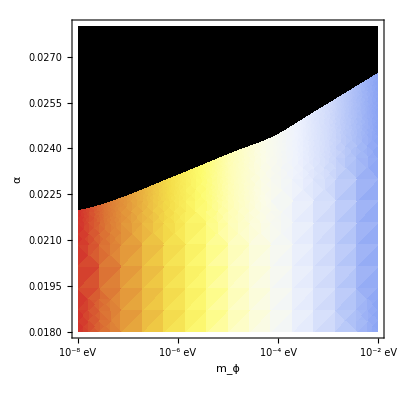
-Graphics-Stable and Unstable Regions of Parameter Space

```mathematica
(*Color version of figure 2, for preprint.*)
cf=(If[#==0,Black,ColorData["TemperatureMap"][(#-Floor[Min[Select[Last/@Flatten[array,1],#>0&]],5])/(Ceiling[Max[#],5]-Floor[Min[#],5]&[Select[Last/@Flatten[array,1],#>0&]])]]&);
Labeled[FullGraphics@GraphicsRow[{DensityPlot[interiorfunc[mp],{mp,-8,-2},{a,.018,.028},RegionFunction->Function[{mp,a},a≤borderfunc[mp]],Epilog->RegionPlot[a≥borderfunc[mp],{mp,-8,-2},{a,.018,.028},PlotStyle->Black,BoundaryStyle->None][[1]],FrameTicks->{{#,Row[{Superscript[10,#]," eV"}]}&/@Table[i,{i,-8,-2,2}],Automatic},FrameLabel->{Subscript[m,ϕ],Rotate[α,-Pi/2]},ColorFunctionScaling->False,ColorFunction->cf],ImageCrop[ImageCrop[Graphics[{White,Rectangle[{0,0},{.01,-.1}],Black,Rectangle[{-.018,0},{-.011,-.007}],Text["Unstable",{.006,-.005}],Inset[BarLegend[{cf,{Floor[Min[#],5],Ceiling[Max[#],5]}&[Select[Last/@Flatten[array,1],#>0&]]},LegendLabel->Superscript[L,eq],Ticks->({#,Row[{Superscript["10",#]," erg/s"}]}&/@(Table[i,{i,Floor[Min[#],5],Ceiling[Max[#],5],5}]&[Select[Last/@Flatten[array,1],#>0&]]))],{0,.07}]},ImageSize->Medium]],{150,600},Top,Padding->White]}],"Stable and Unstable Regions of Parameter Space",Top]
```

```mathematica
(*Color version of figure 3, for preprint.*)
Interpolation[Select[Flatten[array2-Table[{0,1},{mp,-8,-2,.25},{a,.02,.03,.0005}],1],NumberQ[Last[#]]&]];
Labeled[ImageCrop[Plot3D[%[mp,a],{mp,-8,-2},{a,.018,.028},RegionFunction->Function[{mp,a},a≤borderfunc[mp]],PlotRange->All,AxesLabel->{Subscript[m,ϕ],α,Rotate[Row[{Superscript[L,eq]/Superscript[L,"eq,RK"],-1}],.05]},ViewPoint->{-.2,-1.3,1.3},AxesEdge->{{-1,-1},{1,-1},{-1,1}},Boxed->{Back,Left},Ticks->{{#,Row[{Superscript[10,#]," eV"}]}&/@Table[i,{i,-8,-2,3}],Automatic,Automatic},Mesh->None],{720,580},Padding->White],"Schwinger Enhancement to the Equilibrium Luminosity",Top]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

-Graphics-Schwinger Enhancement to the Equilibrium Luminosity